# Setup

```mathematica
(* ================================================================ *)
(* MODULE 0: SETUP                                                  *)
(* ================================================================ *)

baseDir = NotebookDirectory[];
Get[FileNameJoin[{baseDir, "QKT_full.wl"}]];
$HistoryLength = 0;
EnsureDir[dir_] := If[!DirectoryQ[dir],
  CreateDirectory[dir, CreateIntermediateDirectories -> True]];
kStr[k_] := StringReplace[
  If[StringEndsQ[#, "."], # <> "0", #] &[ToString[N[k]]], "." -> "_"];
```

```mathematica
LaunchKernels[14];
```

# Kicked ising

## Model

```mathematica
J=1.0;hz=0.8090;hx=0.9045;tau=1.0;
```

```mathematica
J=1.0;hz=0.8;hx=0.9;tau=1.0;
```

```mathematica
J=Pi/4;hz=0.0;hx=Pi/4;tau=1.0;
```

```mathematica
Off[MakeExpression::boxfmt]

(* ============================================================ *)
(*  Mixed-Field Ising Model — Floquet texture test               *)
(* ============================================================ *)

L  = 10;            (* number of spins, dim = 2^L = 1024 *)
J  = 1.0;
hz = 0.8;        (* Kim-Huse chaotic parameters *)
hx = 0.9;
tau = 1.0;
dim = 2^L;
```

```mathematica
(* Pauli matrices *)
Id2 = IdentityMatrix[2];
sx  = {{0, 1}, {1, 0}};
sz  = {{1, 0}, {0, -1}};
(* Single-site operator embedded in the L-site space *)
op[mat_, i_, len_] := 
  KroneckerProduct @@ Table[If[k == i, mat, Id2], {k, 1, len}];
(* Diagonal part: Ising + longitudinal field, open BC *)
Hz = -J Sum[op[sz, i, L] . op[sz, i + 1, L], {i, 1, L - 1}]- hz Sum[op[sz, i, L], {i, 1, L}];
(* Off-diagonal part: transverse field *)
Hx = -hx Sum[op[sx, i, L], {i, 1, L}];
```

```mathematica
diagHz   = Normal[Diagonal[Hz]];
expHz    = DiagonalMatrix[Exp[-I tau diagHz]];
sqrtHz   = DiagonalMatrix[Exp[-I tau diagHz/2]];
expHx    = MatrixExp[-I tau Hx];

UF    = expHz . expHx;
UFsym = sqrtHz . expHx . sqrtHz;
```

```mathematica
{eval1, vec1} = Eigensystem[UF];
{eval2, vec2} = Eigensystem[UFsym];
```

```mathematica
vec1[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0.0159771,-0.00532574,-0.0126607,-0.0318359,0.0050224,-0.00580577,-0.0325557,-0.0133318,-0.0387202,0.00117526,0.0209739,0.0195438,0.00939889,-0.0069855,-0.0514913,0.00372259,-0.000153958,0.015647,0.00738699,-0.0212313}

```mathematica
vec2[[1]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Entanglement

```mathematica
EntanglementEntropySVD[psi_, dA_, dB_] :=
  Module[{mat, sv2},
    mat = ArrayReshape[psi, {dA, dB}];
    sv2 = SingularValueList[mat]^2;
    (* Hard threshold at machine epsilon level *)
    sv2 = Select[sv2, # > 1.*^-14 &];
    (* Renormalize to absorb discarded numerical noise *)
    sv2 = sv2 / Total[sv2];
    -sv2 . Log[sv2]
  ]
```

```mathematica
entanglement=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec1}];
```

```mathematica
entanglement2=ParallelTable[EntanglementEntropySVD[i, L/2,L/2 ],{i,vec2}];
```

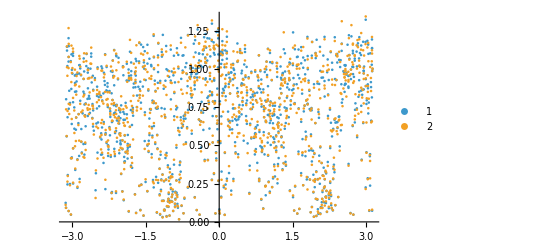

```mathematica
ListPlot[{Transpose[{Arg[eval1],entanglement}],Transpose[{Arg[eval2],entanglement2}]},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
PageEntropy[La_,Lb_]:=N[PolyGamma[0,2^La*2^Lb+1]-PolyGamma[0,2^Lb+1]-(2^La-1)/(2*2^Lb)]
```

```mathematica
La=L/2;
Lb=L/2;
```

```mathematica
Print["dA, dB = ",{2^La,2^Lb}];
Print["Max possible entropy = ",N[Log[Min[2^La,2^Lb]]]];
Print["Page value = ",PageEntropy[La,Lb]];
```

dA, dB = {32,32}

Max possible entropy = 3.46574

Page value = 2.96631

```mathematica
Print["Mean Schmidt rank: ",Mean[Length[Select[SingularValueList[ArrayReshape[#,{2^La,2^Lb}]]^2,#>10^-14&]]&/@vec1]];
```

Mean Schmidt rank: 16381/512

```mathematica
phases=Mod[Arg[eval1],2 Pi];
spacings=Differences[Sort[phases]];
ratios=Min[#1/#2,#2/#1]&@@@Partition[spacings,2,1];
Mean[ratios]
```

0.384444

```mathematica
{J,hz,hx,tau} (*print these to verify*)
```

{1.,0.5,1.4,1.}

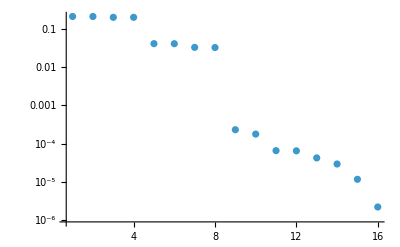

```mathematica
sv=SingularValueList[ArrayReshape[vec1[[1]],{64,64}]];
ListLogPlot[sv^2,PlotRange->All]
```

## Reflection sectors

```mathematica
(* ============================================================ *)
(*  Reflection-sector diagonalization                            *)
(* ============================================================ *)

(* Build orthonormal bases for P=±1 sectors explicitly *)
buildSectorBases[L_] := Module[
  {dim = 2^L, refl, evenB = {}, oddB = {}, seen, r},
  refl[k_] := FromDigits[Reverse[IntegerDigits[k - 1, 2, L]], 2] + 1;
  seen = ConstantArray[False, dim];
  Do[
    If[! seen[[i]],
     r = refl[i];
     seen[[i]] = True; seen[[r]] = True;
     If[i == r,
      AppendTo[evenB, SparseArray[{i -> 1.}, dim]],
      AppendTo[evenB, SparseArray[{i -> 1./Sqrt[2.], r -> 1./Sqrt[2.]}, dim]];
      AppendTo[oddB,  SparseArray[{i -> 1./Sqrt[2.], r -> -1./Sqrt[2.]}, dim]]
      ]
     ], {i, dim}];
  <|"Even" -> Normal /@ evenB, "Odd" -> Normal /@ oddB|>
];

bases = buildSectorBases[L];
BE = bases["Even"];   (* dE × dim *)
BO = bases["Odd"];    (* dO × dim *)
dE = Length[BE]; dO = Length[BO];

(* Project Floquet operators (basis is real, so Transpose = ConjugateTranspose) *)
UFe  = BE . UF . Transpose[BE];
UFo  = BO . UF . Transpose[BO];
UFse = BE . UFsym . Transpose[BE];
UFso = BO . UFsym . Transpose[BO];

{evalE,  vecE}  = Eigensystem[UFe];
{evalO,  vecO}  = Eigensystem[UFo];
{evalSE, vecSE} = Eigensystem[UFse];
{evalSO, vecSO} = Eigensystem[UFso];

(* Re-expand sector eigenvectors into the full 2^L computational basis *)
vecEfull  = vecE  . BE;
vecOfull  = vecO  . BO;
vecSEfull = vecSE . BE;
vecSOfull = vecSO . BO;
```

```mathematica
(*Reflection operator: |s1 s2... sL⟩-> |sL... s2 s1⟩*)P=SparseArray[Table[{i,FromDigits[Reverse[IntegerDigits[i-1,2,L]],2]+1}->1,{i,dim}],{dim,dim}];
```

```mathematica
(* ============================================================ *)
(*  Numerical verification of reflection-sector decomposition   *)
(* ============================================================ *)

(* Test 1: P commutes with UF and UFsym *)
Print["[1] ||[P, UF]||_max  = ",
  Max[Abs[P . UF - UF . P]] // N]
Print["[1] ||[P, UFsym]||_max = ",
  Max[Abs[P . UFsym - UFsym . P]] // N]

(* Test 2: Basis orthonormality *)
Print["[2] ||BE.BE^T - I_dE||_max = ",
  Max[Abs[BE . Transpose[BE] - IdentityMatrix[dE]]] // N]
Print["[2] ||BO.BO^T - I_dO||_max = ",
  Max[Abs[BO . Transpose[BO] - IdentityMatrix[dO]]] // N]

(* Test 3: Resolution of identity *)
Print["[3] ||BE^T.BE + BO^T.BO - I_dim||_max = ",
  Max[Abs[Transpose[BE] . BE + Transpose[BO] . BO - 
         IdentityMatrix[dim]]] // N]

(* Test 4: Basis vectors are P eigenstates *)
Print["[4] ||P.BE^T - BE^T||_max (even, +1) = ",
  Max[Abs[P . Transpose[BE] - Transpose[BE]]] // N]
Print["[4] ||P.BO^T + BO^T||_max (odd, -1)  = ",
  Max[Abs[P . Transpose[BO] + Transpose[BO]]] // N]

(* Test 5: Sector matrix eigenvalues match full spectrum *)
evFull   = Sort[Mod[Arg[Eigenvalues[UF]],    2 Pi]];
evSector = Sort[Mod[Arg[Join[evalE, evalO]], 2 Pi]];
Print["[5] ||full spectrum - sector spectrum||_max = ",
  Max[Abs[evFull - evSector]] // N]

(* Test 6: Re-expanded eigenvectors have correct parity *)
Print["[6] max |<psi_E|P|psi_E> - 1| (even, sample 10) = ",Max[Abs[Table[Conjugate[vecEfull[[k]]].P.vecEfull[[k]]-1,{k,1,Min[10,dE]}]]]//N]

Print["[6] max |<psi_O|P|psi_O> + 1| (odd, sample 10) = ",
Max[Abs[Table[Conjugate[vecOfull[[k]]].P.vecOfull[[k]]+1,{k,1,Min[10,dO]}]]]//N]

(* Test 7: UFsym sector eigenvectors are real *)
Print["[7] max |Im(vecSE)| = ", Max[Abs[Im[vecSE]]] // N]
Print["[7] max |Im(vecSO)| = ", Max[Abs[Im[vecSO]]] // N]

(* Test 8: Sector matrices reproduce UF on full basis *)
Print["[8] ||BE^T.UFe.BE + BO^T.UFo.BO - UF||_max = ",
  Max[Abs[Transpose[BE] . UFe . BE + 
          Transpose[BO] . UFo . BO - UF]] // N]
```

[1] ||[P, UF]||_max  = 1.0718×10^-15

[1] ||[P, UFsym]||_max = 1.0716×10^-15

[2] ||BE.BE^T - I_dE||_max = 2.22045×10^-16

[2] ||BO.BO^T - I_dO||_max = 2.22045×10^-16

[3] ||BE^T.BE + BO^T.BO - I_dim||_max = 2.22045×10^-16

[4] ||P.BE^T - BE^T||_max (even, +1) = 0.

[4] ||P.BO^T + BO^T||_max (odd, -1)  = 0.

[5] ||full spectrum - sector spectrum||_max = 1.5099×10^-14

[6] max |<psi_E|P|psi_E> - 1| (even, sample 10) = 2.22045×10^-15

[6] max |<psi_O|P|psi_O> + 1| (odd, sample 10) = 1.77636×10^-15

[7] max |Im(vecSE)| = 5.43772×10^-13

[7] max |Im(vecSO)| = 3.21325×10^-13

[8] ||BE^T.UFe.BE + BO^T.UFo.BO - UF||_max = 5.37685×10^-16

```mathematica
La=L/2;
Lb=L/2;
```

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];
phasesE = Mod[Arg[evalE], 2 Pi];
ratiosE = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesE]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosE], " (expect ~0.527 for COE)"];
(* Entanglement in even sector *)
entEven = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecEfull}];
Print["Mean entanglement (even sector) = ", Mean[entEven],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.528788 (expect ~0.527 for COE)

Mean entanglement (even sector) = 2.87648   Page = 2.96631

```mathematica
(* Sanity checks *)
Print["Sector dims: even = ", dE, ", odd = ", dO, ", total = ", dE + dO];
phasesO = Mod[Arg[evalO], 2 Pi];
ratiosO = Min[#1/#2, #2/#1] & @@@ 
   Partition[Differences[Sort[phasesO]], 2, 1];
Print["<r> in even sector = ", Mean[ratiosO], " (expect ~0.527 for COE)"];
(* Entanglement in even sector *)
entOdd = ParallelTable[EntanglementEntropySVD[v, 2^La, 2^Lb], {v, vecSOfull}];
Print["Mean entanglement (odd sector) = ", Mean[entOdd],
      "   Page = ", PageEntropy[La, Lb]];
```

Sector dims: even = 528, odd = 496, total = 1024

<r> in even sector = 0.522386 (expect ~0.527 for COE)

Mean entanglement (odd sector) = 2.88712   Page = 2.96631

# Texture non-sym

```mathematica
(* ------------------------------------------------------------ *)
(*  Single-realization eigensystem within sectors               *)
(* ------------------------------------------------------------ *)
GetKIEigensystem[hx_] := Module[
  {Hxloc, expHxloc, UFloc, UFeloc, UFoloc, esE, esO, phE, phO},
  Hxloc    = -hx Sum[op[sx, i, L], {i, 1, L}];
  expHxloc = MatrixExp[-I tau Hxloc];
  UFloc    = expHz . expHxloc;         (* expHz fixed *)
  UFeloc   = BE . UFloc . Transpose[BE];
  UFoloc   = BO . UFloc . Transpose[BO];
  esE = Eigensystem[UFeloc];
  esO = Eigensystem[UFoloc];
  phE = Sort[Mod[Arg[esE[[1]]], 2 Pi]];
  phO = Sort[Mod[Arg[esO[[1]]], 2 Pi]];
  <|"Even" -> <|"Phases" -> phE, "Vectors" -> esE[[2, Ordering[phE]]]|>,
    "Odd"  -> <|"Phases" -> phO, "Vectors" -> esO[[2, Ordering[phO]]]|>|>
];
```

```mathematica
(* ============================================================ *)
(*  Kicked Ising — Ensemble for Texture and SFF                  *)
(* ============================================================ *)

nEns    = 50;
hxCenter = 0.9045;
delta   = 0.005;
hxList  = RandomReal[{hxCenter - delta, hxCenter + delta}, nEns];

(* Build sector bases once — fixed for all realizations *)
bases = buildSectorBases[L];
BE = bases["Even"];
BO = bases["Odd"];
dE = Length[BE];
dO = Length[BO];

(* Uniform textureless state within each sector *)
f1E = ConstantArray[1./Sqrt[dE], dE];
f1O = ConstantArray[1./Sqrt[dO], dO];
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Generate ensemble                                            *)
(* ------------------------------------------------------------ *)

DistributeDefinitions[GetKIEigensystem, buildSectorBases,
  expHz, BE, BO, op, sz, sx, Id2, J, hz, tau, L];
```

```mathematica
Print["Generating ", nEns, " realizations..."];
rawEns = ParallelTable[GetKIEigensystem[hx], {hx, hxList},
  Method -> "CoarsestGrained"];
(* Structure ensemble per sector *)
kiEnsemble = <|
  "Even" -> Table[<|"Phases" -> d["Even","Phases"],
                    "Vectors" -> d["Even","Vectors"]|>, {d, rawEns}],
  "Odd"  -> Table[<|"Phases" -> d["Odd","Phases"],
                    "Vectors" -> d["Odd","Vectors"]|>, {d, rawEns}]|>;
```

Generating 50 realizations...

```mathematica
allevenvecs=kiEnsemble["Even"][[1]]["Vectors"];
alloddvecs=kiEnsemble["Odd"][[1]]["Vectors"];
```

```mathematica
allevenvecs//Dimensions
alloddvecs//Dimensions
```

{528,528}

{496,496}

```mathematica
allevenvecs[[1]][[1;;-1;;50]]//Im//Chop
alloddvecs[[1]][[1;;-1;;50]]//Im//Chop
```

{-0.0080592,0.0214508,0.000280947,-0.0193588,-0.043758,0,-0.0628832,-0.0227005,-0.0338511,-0.0102346,-0.0642269}

{0.00354038,0.0134811,0.0119525,-0.00260451,0.0137767,-0.00861336,0.00275923,0.0180507,0.0043119,-0.0136078}

```mathematica
(* ------------------------------------------------------------ *)
(*  Texture                                                      *)
(* ------------------------------------------------------------ *)
EnsembleTexSector[ensembleList_, f1_, tMax_] := Module[
  {nMat = Length[ensembleList], tGrid = Range[0, tMax], allTex},
  DistributeDefinitions[tGrid, f1];
  allTex = ParallelTable[
    Module[{ph = ensembleList[[i,"Phases"]], vecs = ensembleList[[i,"Vectors"]], 
            d, pArr},
      d = Length[ph];
      pArr = Abs[Conjugate[vecs] . f1]^2;
      Table[d * Abs[Total[pArr * Exp[-I t ph]]]^2, {t, tGrid}]
    ], {i, nMat}, Method -> "CoarsestGrained"];
  <|"Time" -> tGrid, "AllTex" -> allTex, "MeanTex" -> Mean[allTex]|>
];
```

```mathematica
tMaxTex = 2000;
sigmaSm = 10;

Print["Computing texture — Even sector..."];
texE = EnsembleTexSector[kiEnsemble["Even"], f1E, tMaxTex];
Print["Computing texture — Odd sector..."];
texO = EnsembleTexSector[kiEnsemble["Odd"],  f1O, tMaxTex];

texEsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texE["AllTex"]]];
texOsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texO["AllTex"]]];
```

Computing texture — Even sector...

Computing texture — Odd sector...

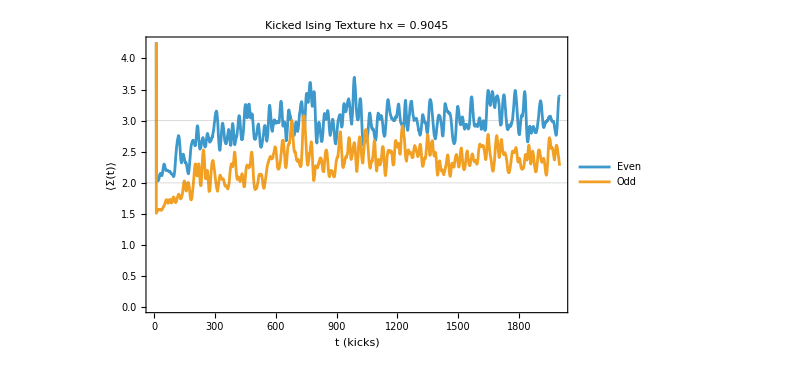

```mathematica
ListLinePlot[
  {Transpose[{texE["Time"], texEsm}],
   Transpose[{texO["Time"], texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

```mathematica
(* Heisenberg units: t/t_H where t_H = sector dimension *)
tHE = dE;
tHO = dO;

tGridHE = texE["Time"] / tHE;
tGridHO = texO["Time"] / tHO;
```

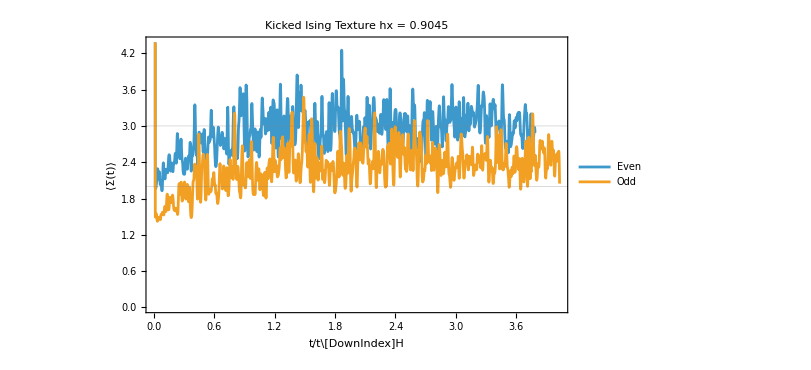

```mathematica
(* Linear plot in Heisenberg units *)
pLin = ListLinePlot[
  {Transpose[{tGridHE, texEsm}],
   Transpose[{tGridHO, texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t/t\[DownIndex]H", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

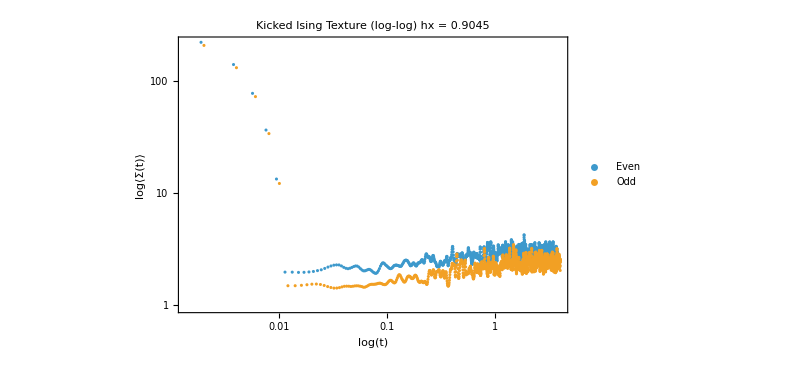

```mathematica
(* Log-log plot — drop t=0 to avoid Log[0] *)
tSkip = 2;  (* skip first few points *)
pLog = ListLogLogPlot[
  {Transpose[{tGridHE[[tSkip;;]], texEsm[[tSkip;;]]}],
   Transpose[{tGridHO[[tSkip;;]], texOsm[[tSkip;;]]}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"log(t)", "log⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture (log-log)  hx = " <> ToString[hxCenter], 14]
]
```

# Texture sym

```mathematica
(* ------------------------------------------------------------ *)
(*  Single-realization eigensystem within sectors               *)
(* ------------------------------------------------------------ *)
GetKIEigensystem[hx_] := Module[
  {Hxloc, expHxloc, UFloc, UFeloc, UFoloc, esE, esO, phE, phO},
  Hxloc    = -hx Sum[op[sx, i, L], {i, 1, L}];
  expHxloc = MatrixExp[-I tau Hxloc];
  UFloc    = sqrtHz . expHx . sqrtHz;         (* expHz fixed *)
  UFeloc   = BE . UFloc . Transpose[BE];
  UFoloc   = BO . UFloc . Transpose[BO];
  esE = Eigensystem[UFeloc];
  esO = Eigensystem[UFoloc];
  phE = Sort[Mod[Arg[esE[[1]]], 2 Pi]];
  phO = Sort[Mod[Arg[esO[[1]]], 2 Pi]];
  <|"Even" -> <|"Phases" -> phE, "Vectors" -> esE[[2, Ordering[phE]]]|>,
    "Odd"  -> <|"Phases" -> phO, "Vectors" -> esO[[2, Ordering[phO]]]|>|>
];
```

```mathematica
(* ============================================================ *)
(*  Kicked Ising — Ensemble for Texture and SFF                  *)
(* ============================================================ *)
nEns    = 100;
hxCenter = 0.9;
delta   = 0.005;
hxList  = RandomReal[{hxCenter - delta, hxCenter + delta}, nEns];

(* Build sector bases once — fixed for all realizations *)
bases = buildSectorBases[L];
BE = bases["Even"];
BO = bases["Odd"];
dE = Length[BE];
dO = Length[BO];

(* Uniform textureless state within each sector *)
f1E = ConstantArray[1./Sqrt[dE], dE];
f1O = ConstantArray[1./Sqrt[dO], dO];
```

```mathematica
(* ------------------------------------------------------------ *)
(*  Generate ensemble                                            *)
(* ------------------------------------------------------------ *)
DistributeDefinitions[GetKIEigensystem, buildSectorBases,
  expHz,sqrtHz,BE, BO, op, sz, sx, Id2, J, hz, tau, L];
```

```mathematica
Print["Generating ", nEns, " realizations..."];
rawEns = ParallelTable[GetKIEigensystem[hx], {hx, hxList},
  Method -> "CoarsestGrained"];
(* Structure ensemble per sector *)
kiEnsemble = <|
  "Even" -> Table[<|"Phases" -> d["Even","Phases"],
                    "Vectors" -> d["Even","Vectors"]|>, {d, rawEns}],
  "Odd"  -> Table[<|"Phases" -> d["Odd","Phases"],
                    "Vectors" -> d["Odd","Vectors"]|>, {d, rawEns}]|>;
```

Generating 100 realizations...

```mathematica
allevenvecs=kiEnsemble["Even"][[1]]["Vectors"];
alloddvecs=kiEnsemble["Odd"][[1]]["Vectors"];
```

```mathematica
allevenvecs//Dimensions
alloddvecs//Dimensions
```

{528,528}

{496,496}

```mathematica
allevenvecs[[10]][[1;;-1;;50]]//Im//Chop
alloddvecs[[10]][[1;;-1;;50]]//Im//Chop
```

{0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

```mathematica
(* ------------------------------------------------------------ *)
(*  Texture                                                      *)
(* ------------------------------------------------------------ *)
EnsembleTexSector[ensembleList_, f1_, tMax_] := Module[
  {nMat = Length[ensembleList], tGrid = Range[0, tMax], allTex},
  DistributeDefinitions[tGrid, f1];
  allTex = ParallelTable[
    Module[{ph = ensembleList[[i,"Phases"]], vecs = ensembleList[[i,"Vectors"]], 
            d, pArr},
      d = Length[ph];
      pArr = Abs[Conjugate[vecs] . f1]^2;
      Table[d * Abs[Total[pArr * Exp[-I t ph]]]^2, {t, tGrid}]
    ], {i, nMat}, Method -> "CoarsestGrained"];
  <|"Time" -> tGrid, "AllTex" -> allTex, "MeanTex" -> Mean[allTex]|>
];
```

```mathematica
tMaxTex = 2000;
sigmaSm = 10;

Print["Computing texture — Even sector..."];
texE = EnsembleTexSector[kiEnsemble["Even"], f1E, tMaxTex];
Print["Computing texture — Odd sector..."];
texO = EnsembleTexSector[kiEnsemble["Odd"],  f1O, tMaxTex];

texEsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texE["AllTex"]]];
texOsm = Mean[Map[GaussianFilter[#, sigmaSm]&, texO["AllTex"]]];
```

Computing texture — Even sector...

Computing texture — Odd sector...

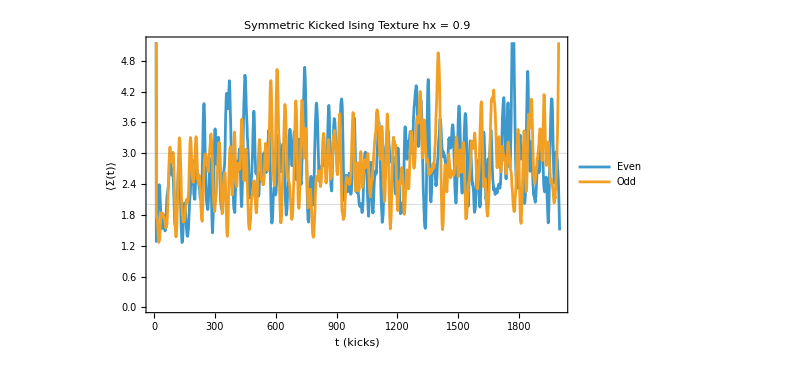

```mathematica
ListLinePlot[
  {Transpose[{texE["Time"], texEsm}],
   Transpose[{texO["Time"], texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t (kicks)", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Symmetric Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

```mathematica
(* Heisenberg units: t/t_H where t_H = sector dimension *)
tHE = dE;
tHO = dO;

tGridHE = texE["Time"] / tHE;
tGridHO = texO["Time"] / tHO;
```

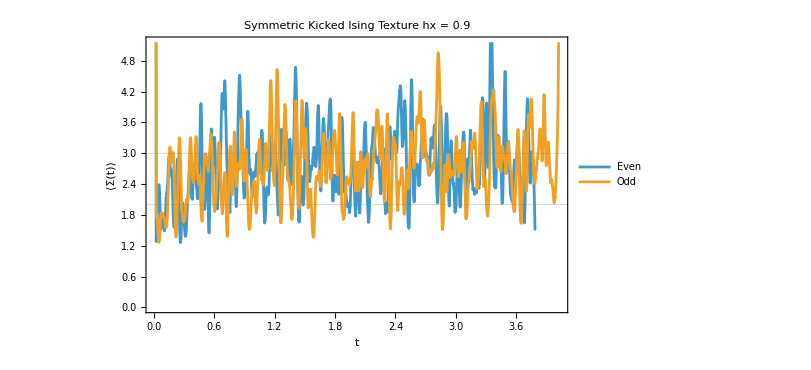

```mathematica
(* Linear plot in Heisenberg units *)
pLin = ListLinePlot[
  {Transpose[{tGridHE, texEsm}],
   Transpose[{tGridHO, texOsm}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"t", "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Symmetric Kicked Ising Texture  hx = " <> ToString[hxCenter], 14]
]
```

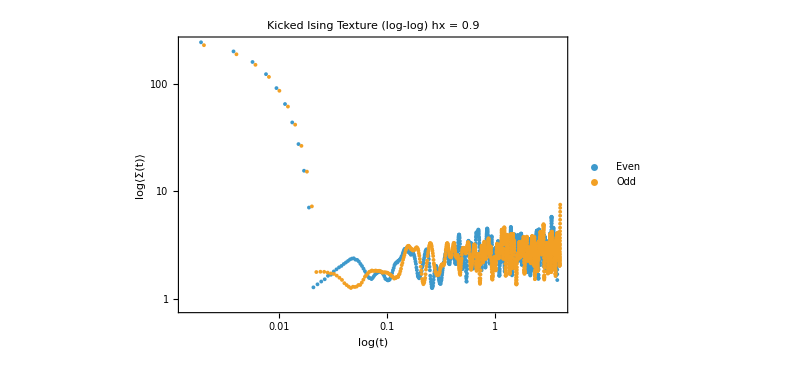

```mathematica
(* Log-log plot — drop t=0 to avoid Log[0] *)
tSkip = 2;  (* skip first few points *)
pLog = ListLogLogPlot[
  {Transpose[{tGridHE[[tSkip;;]], texEsm[[tSkip;;]]}],
   Transpose[{tGridHO[[tSkip;;]], texOsm[[tSkip;;]]}]},
  PlotLegends -> {"Even", "Odd"},
  FrameLabel -> {"log(t)", "log⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Kicked Ising Texture (log-log)  hx = " <> ToString[hxCenter], 14]
]
```

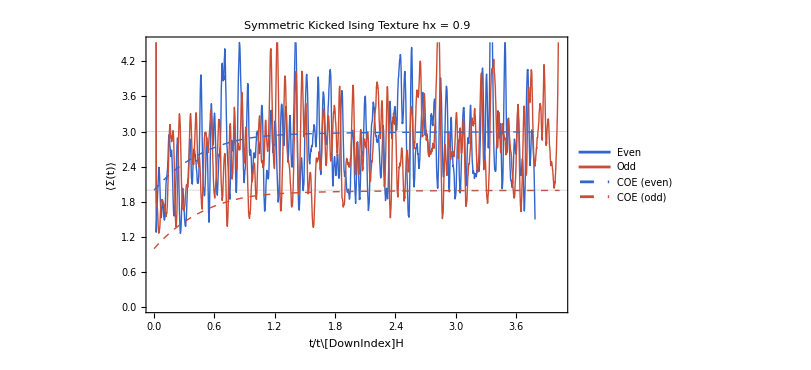

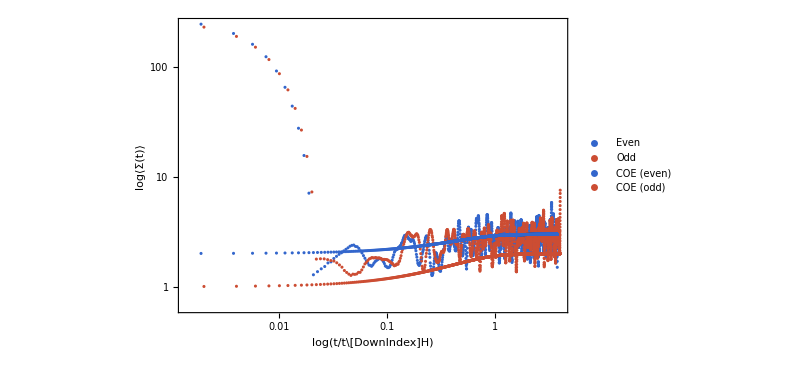

```mathematica
(* Analytical predictions in Heisenberg units *)
texCOEanE = Table[2 + COESFFAnalytical[t], {t, tGridHE}];
texCOEanO = Table[1 + COESFFAnalytical[t], {t, tGridHO}];

pLin = ListLinePlot[
  {Transpose[{tGridHE, texEsm}],
   Transpose[{tGridHO, texOsm}],
   Transpose[{tGridHE, texCOEanE}],
   Transpose[{tGridHO, texCOEanO}]},
  PlotLegends -> {"Even", "Odd", "COE (even)", "COE (odd)"},
  PlotStyle -> {
    Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
    Directive[Thick, RGBColor[0.8, 0.3, 0.2]],
    Directive[Thick, Dashed, RGBColor[0.2, 0.4, 0.8]],
    Directive[Thick, Dashed, RGBColor[0.8, 0.3, 0.2]]},
  FrameLabel -> {"t/t\[DownIndex]H",
    "⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600,
  PlotLabel -> Style["Symmetric Kicked Ising Texture  hx = " <>
    ToString[hxCenter], 14]
]

pLog = ListLogLogPlot[
  {Transpose[{tGridHE[[2;;]], texEsm[[2;;]]}],
   Transpose[{tGridHO[[2;;]], texOsm[[2;;]]}],
   Transpose[{tGridHE[[2;;]], texCOEanE[[2;;]]}],
   Transpose[{tGridHO[[2;;]], texCOEanO[[2;;]]}]},
  PlotLegends -> {"Even", "Odd", "COE (even)", "COE (odd)"},
  PlotStyle -> {
    Directive[Thick, RGBColor[0.2, 0.4, 0.8]],
    Directive[Thick, RGBColor[0.8, 0.3, 0.2]],
    Directive[Thick, Dashed, RGBColor[0.2, 0.4, 0.8]],
    Directive[Thick, Dashed, RGBColor[0.8, 0.3, 0.2]]},
  FrameLabel -> {"log(t/t\[DownIndex]H)",
    "log⟨Σ(t)⟩"},
  GridLines -> {None, {2, 3}},
  Frame -> True, ImageSize -> 600
]
```